CClear[Global`*]

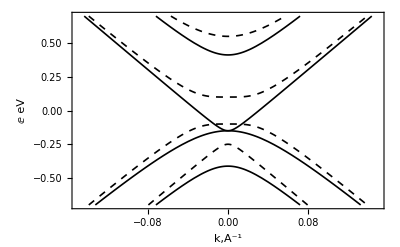

```mathematica
CClear["Global`*"]
tp=0.4; c=6.25;d=0.1;
f1[x_]=Sqrt[d^2+(c*x)^2+tp^2/2+tp*(tp^2/4+(c*x)^2)^(1/2)];
f2[x_]=-Sqrt[d^2+(c*x)^2+tp^2/2+tp*(tp^2/4+(c*x)^2)^(1/2)];
f3[x_]=-Sqrt[d^2+(c*x)^2+tp^2/2-tp*(tp^2/4+(c*x)^2)^(1/2)];
f4[x_]=Sqrt[d^2+(c*x)^2+tp^2/2-tp*(tp^2/4+(c*x)^2)^(1/2)];
v1[x_]=tp/2+Sqrt[(c*x)^2+(tp/2+d1)^2];
v2[x_]=tp/2-Sqrt[(c*x)^2+(tp/2+d1)^2];
v3[x_]=-tp/2+Sqrt[(c*x)^2+(tp/2-d1)^2];
v4[x_]=-tp/2-Sqrt[(c*x)^2+(tp/2-d1)^2];

Plot[{f1[x],f2[x],f3[x],f4[x],v1[x],v2[x],v3[x],v4[x]},{x,-0.15,0.15},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},{PlotStyle->{{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed}}},Frame->True]
```

```mathematica
Export["f1.pdf",Plot[{f1[x],f2[x],f3[x],f4[x],v1[x],v2[x],v3[x],v4[x]},{x,-0.15,0.15},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},{PlotStyle->{{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed}}},Frame->True]]
```

f1.pdf

```mathematica
Manipulate[Plot[{f3[x,d],f4[x,d]},{x,-0.15,0.15},PlotRange->{-0.7,0.7}],{d,-0.2,0.2}]
```